## Functions

As we saw in the previous lectures, the Map function needs another function to map over the list of values. We had our named function fib that we mapped over the list. Sometimes, we need a quick function and we don’t want to explicitly give it a name. We call these anonymous functions, or pure functions.

### Pure Functions

Pure functions are functions defined inline. Let’s take a look at pure functions:

```mathematica
?Function
```

RowBox[{"Function", "[", StyleBox["body", "TI"], "]"}] or RowBox[{StyleBox["body", "TI"], "&"}] is a pure function. The formal parameters are # (or #1), #2, etc. 
RowBox[{"Function", "[", RowBox[{StyleBox["x", "TI"], ",", StyleBox["body", "TI"]}], "]"}] is a pure function with a single formal parameter StyleBox["x", "TI"]. 
RowBox[{"Function", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["body", "TI"]}], "]"}] is a pure function with a list of formal parameters.

A pure function is a piece of code wrapped with the head Function. The arguments to the function are the hash symbol, which in Mathematica is called Slot:

```mathematica
?Slot
```

# represents the first argument supplied to a pure function. 
StyleBox[RowBox[{"#", StyleBox["n", "TI"]}]] represents the StyleBox[RowBox[{StyleBox["n", "TI"], ""}]]SuperscriptBox["", "th"] argument. 
StyleBox[RowBox[{"#", StyleBox["name", "TI"]}]] represents the value associated with key "
StyleBox["name", "TI"]" in an association in the first argument.

A simple pure function that increments a value would look like this:

```mathematica
Function[#+1]
```

#1+1&

Here, Mathematica converted it to the shorthand notation, which we can also use:

```mathematica
#+1&
```

#1+1&

Pure functions can be called just like regular functions, using the square bracket notation:

```mathematica
#+1&[3]
```

4

Here, we passed the value 3 to our function, which incremented it and returned 4. We could have also written it as follows:

```mathematica
incr=Function[#+1]
```

#1+1&

And we can use our new incr function just like any other function:

```mathematica
incr[3]
```

4

Let’s use Map with a pure function to increment every value in our range list by 1. Here’s our range list:

```mathematica
range
```

{1,2,3,4,5,6,7,8,9,10,11,12}

Now we map our pure function over the values in range:

```mathematica
Map[Function[#+1],range]
```

{2,3,4,5,6,7,8,9,10,11,12,13}

Recall the shorthand for Map:

```mathematica
Function[#+1]/@range
```

{2,3,4,5,6,7,8,9,10,11,12,13}

We can also use the shorthand for pure functions with Map:

```mathematica
Map[#+1&,range]
```

{2,3,4,5,6,7,8,9,10,11,12,13}

And now combining them both:

```mathematica
#+1&/@range
```

{2,3,4,5,6,7,8,9,10,11,12,13}

Does this look a little like black magic? Don’t worry if it looks a little scary. This syntax is extremely common in Mathematica. With practice, you’ll be able to read this syntax like a pro, so don’t forget to do the homework.

Note that we could have also achieved this with a replacement rule:

```mathematica
range/.x_Integer:>x+1
```

{2,3,4,5,6,7,8,9,10,11,12,13}

In many cases, you can use a replacement rule instead of a pure function with the Map function. Can you think of a case where you might not be able to do this?

Could you think of an example? Remember that Map applies the function to the first level in the expression, whereas replacement rules are applied to any expression that matches the pattern, regardless of the level. So for example:

```mathematica
Map[f,{1,2,3,{1,2,3}}]
```

{f[1],f[2],f[3],f[{1,2,3}]}

Applies f to each element at the top level of the expression, however, the rule replacement that achieves the same thing would be awkward to write. The naive approach doesn’t have the exact same behavior:

```mathematica
{1,2,3,{1,2,3}}/.n_Integer:>f[n]
```

{f[1],f[2],f[3],{f[1],f[2],f[3]}}

Here, f was applied to the integers inside the sublist; the replacement rule was not limited to the top level of the expression. In this particular case, we can achieve our goal by adding another rule:

```mathematica
{1,2,3,{1,2,3}}/.{n_Integer:>f[n],s:{___Integer}:>f[s]}
```

{f[1],f[2],f[3],f[{1,2,3}]}

Note that this rule replacement works only for this particular input. In general you’ll have to be creative with your rule replacement to replicate the behavior of Map.

Let’s look at another example of a pure function. Consider our nestedRange:

```mathematica
nestedRange=Partition[Range[12],4]
```

{{1,2,3,4},{5,6,7,8},{9,10,11,12}}

Let’s write a function that will swap the first and last values of each sublist so that we end up with:

```mathematica
{{4,2,3,1},{8,6,7,5},{12,10,11,9}}
```

{{4,2,3,1},{8,6,7,5},{12,10,11,9}}

We will be mapping our pure function over the nested range, which means that our pure function will take a single argument, which is a list. We’re going to use the Part function to take the list apart and join it back together using the Join function. Let’s bring up Part for reference:

```mathematica
?Part
```

RowBox[{StyleBox["expr", "TI"], "[", RowBox[{"[", StyleBox["i", "TI"], "]"}], "]"}] or RowBox[{"Part", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["i", "TI"]}], "]"}] gives the StyleBox["i", "TI"]SuperscriptBox["", "th"] part of StyleBox["expr", "TI"]. 
RowBox[{StyleBox["expr", "TI"], "[", RowBox[{"[", RowBox[{"-", StyleBox["i", "TI"]}], "]"}], "]"}] counts from the end. 
RowBox[{StyleBox["expr", "TI"], "[", RowBox[{"[", RowBox[{StyleBox["i", "TI"], ",", StyleBox["j", "TI"], ",", StyleBox["…", "TR"]}], "]"}], "]"}] or RowBox[{"Part", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["i", "TI"], ",", StyleBox["j", "TI"], ",", StyleBox["…", "TR"]}], "]"}] is equivalent to RowBox[{RowBox[{RowBox[{StyleBox["expr", "TI"], "[", RowBox[{"[", StyleBox["i", "TI"], "]"}], "]"}], "[", RowBox[{"[", StyleBox["j", "TI"], "]"}], "]"}], StyleBox["…", "TR"]}]. 
RowBox[{StyleBox["expr", "TI"], "[", RowBox[{"[", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["i", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], "]"}], "]"}] gives a list of the parts SubscriptBox[StyleBox["i", "TI"], StyleBox["1", "TR"]], SubscriptBox[StyleBox["i", "TI"], StyleBox["2", "TR"]], … of StyleBox["expr", "TI"]. 
RowBox[{StyleBox["expr", "TI"], "[", RowBox[{"[", RowBox[{StyleBox["m", "TI"], ";;", StyleBox["n", "TI"]}], "]"}], "]"}] gives parts StyleBox["m", "TI"] through StyleBox["n", "TI"].
RowBox[{StyleBox["expr", "TI"], "[", RowBox[{"[", RowBox[{StyleBox["m", "TI"], ";;", StyleBox["n", "TI"], ";;", StyleBox["s", "TI"]}], "]"}], "]"}] gives parts StyleBox["m", "TI"] through StyleBox["n", "TI"] in steps of StyleBox["s", "TI"].
RowBox[{StyleBox["expr", "TI"], "[", RowBox[{"[", StyleBox["\"\!\(\*StyleBox[\"key\",\"TI\"]\)\"", ShowStringCharacters->True], "]"}], "]"}] gives the value associated with the key "
StyleBox["key", "TI"]" in an association StyleBox["expr", "TI"].
RowBox[{StyleBox["expr", "TI"], "[", RowBox[{"[", RowBox[{"Key", "[", StyleBox["k", "TI"], "]"}], "]"}], "]"}] gives the value associated with an arbitrary key StyleBox["k", "TI"] in the association StyleBox["expr", "TI"].

And the Join function:

```mathematica
?Join
```

RowBox[{"Join", "[", RowBox[{SubscriptBox[StyleBox["list", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["list", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "]"}] concatenates lists or other expressions that share the same head.
RowBox[{"Join", "[", RowBox[{SubscriptBox[StyleBox["list", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["list", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"], ",", StyleBox["n", "TI"]}], "]"}] joins the objects at level StyleBox["n", "TI"] in each of the SubscriptBox[StyleBox["list", "TI"], StyleBox["i", "TI"]].

First, we need to take the last element out of the list, and it needs to be in a list. We’ll use the 4th form of Part to do that:

```mathematica
#[[{-1}]]&
```

#1⟦{-1}⟧&

Let’s test this out using a test list:

```mathematica
#[[{-1}]]&[{a,b,c,d,e}]
```

{e}

Now we need to add the elements b through d, using the 5th form of Part which enables us to express a range of values:

```mathematica
Join[
#[[{-1}]],
#[[2;;-2]]
]&[{a,b,c,d,e}]
```

{e,b,c,d}

And lastly, let’s append the first element to the end:

```mathematica
Join[
#[[{-1}]],
#[[2;;-2]],
#[[{1}]]
]&[{a,b,c,d,e}]
```

{e,b,c,d,a}

Now that we have our pure function, let’s map it over the nested range:

```mathematica
Join[
#[[{-1}]],
#[[2;;-2]],
#[[{1}]]
]&/@nestedRange
```

{{4,2,3,1},{8,6,7,5},{12,10,11,9}}

### Rolling 3 Dice

Great! Let’s do an example that uses the Map function and pure functions. Suppose you have 3 identical 6-sided dice. When you roll the dice, each dice may randomly become any value, 1 through 6. If we take the sum of the three dice, the possible values range from 3 to 18. We get 3 when we roll 3 ones, and we get 18 when we roll 3 sixes. Let’s compute the probability of rolling any of the sums 3 through 18. To start with, let’s create a list of all the possible outcomes (sample space):

```mathematica
outcomes=Tuples[{Range[6],Range[6],Range[6]}]
```

{{1,1,1},{1,1,2},{1,1,3},{1,1,4},{1,1,5},{1,1,6},{1,2,1},{1,2,2},{1,2,3},{1,2,4},{1,2,5},{1,2,6},{1,3,1},{1,3,2},{1,3,3},{1,3,4},{1,3,5},{1,3,6},{1,4,1},{1,4,2},{1,4,3},{1,4,4},{1,4,5},{1,4,6},{1,5,1},{1,5,2},{1,5,3},{1,5,4},{1,5,5},{1,5,6},{1,6,1},{1,6,2},{1,6,3},{1,6,4},{1,6,5},{1,6,6},{2,1,1},{2,1,2},{2,1,3},{2,1,4},{2,1,5},{2,1,6},{2,2,1},{2,2,2},{2,2,3},{2,2,4},{2,2,5},{2,2,6},{2,3,1},{2,3,2},{2,3,3},{2,3,4},{2,3,5},{2,3,6},{2,4,1},{2,4,2},{2,4,3},{2,4,4},{2,4,5},{2,4,6},{2,5,1},{2,5,2},{2,5,3},{2,5,4},{2,5,5},{2,5,6},{2,6,1},{2,6,2},{2,6,3},{2,6,4},{2,6,5},{2,6,6},{3,1,1},{3,1,2},{3,1,3},{3,1,4},{3,1,5},{3,1,6},{3,2,1},{3,2,2},{3,2,3},{3,2,4},{3,2,5},{3,2,6},{3,3,1},{3,3,2},{3,3,3},{3,3,4},{3,3,5},{3,3,6},{3,4,1},{3,4,2},{3,4,3},{3,4,4},{3,4,5},{3,4,6},{3,5,1},{3,5,2},{3,5,3},{3,5,4},{3,5,5},{3,5,6},{3,6,1},{3,6,2},{3,6,3},{3,6,4},{3,6,5},{3,6,6},{4,1,1},{4,1,2},{4,1,3},{4,1,4},{4,1,5},{4,1,6},{4,2,1},{4,2,2},{4,2,3},{4,2,4},{4,2,5},{4,2,6},{4,3,1},{4,3,2},{4,3,3},{4,3,4},{4,3,5},{4,3,6},{4,4,1},{4,4,2},{4,4,3},{4,4,4},{4,4,5},{4,4,6},{4,5,1},{4,5,2},{4,5,3},{4,5,4},{4,5,5},{4,5,6},{4,6,1},{4,6,2},{4,6,3},{4,6,4},{4,6,5},{4,6,6},{5,1,1},{5,1,2},{5,1,3},{5,1,4},{5,1,5},{5,1,6},{5,2,1},{5,2,2},{5,2,3},{5,2,4},{5,2,5},{5,2,6},{5,3,1},{5,3,2},{5,3,3},{5,3,4},{5,3,5},{5,3,6},{5,4,1},{5,4,2},{5,4,3},{5,4,4},{5,4,5},{5,4,6},{5,5,1},{5,5,2},{5,5,3},{5,5,4},{5,5,5},{5,5,6},{5,6,1},{5,6,2},{5,6,3},{5,6,4},{5,6,5},{5,6,6},{6,1,1},{6,1,2},{6,1,3},{6,1,4},{6,1,5},{6,1,6},{6,2,1},{6,2,2},{6,2,3},{6,2,4},{6,2,5},{6,2,6},{6,3,1},{6,3,2},{6,3,3},{6,3,4},{6,3,5},{6,3,6},{6,4,1},{6,4,2},{6,4,3},{6,4,4},{6,4,5},{6,4,6},{6,5,1},{6,5,2},{6,5,3},{6,5,4},{6,5,5},{6,5,6},{6,6,1},{6,6,2},{6,6,3},{6,6,4},{6,6,5},{6,6,6}}

Now, we need to compute the sum of each outcome. We can use the Total function:

```mathematica
?Total
```

RowBox[{"Total", "[", StyleBox["list", "TI"], "]"}] gives the total of the elements in StyleBox["list", "TI"]. 
RowBox[{"Total", "[", RowBox[{StyleBox["list", "TI"], ",", StyleBox["n", "TI"]}], "]"}] totals all elements down to level StyleBox["n", "TI"]. 
RowBox[{"Total", "[", RowBox[{StyleBox["list", "TI"], ",", RowBox[{"{", StyleBox["n", "TI"], "}"}]}], "]"}] totals elements at level StyleBox["n", "TI"]. 
RowBox[{"Total", "[", RowBox[{StyleBox["list", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["n", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["n", "TI"], StyleBox["2", "TR"]]}], "}"}]}], "]"}] totals elements at levels SubscriptBox[StyleBox["n", "TI"], StyleBox["1", "TR"]] through SubscriptBox[StyleBox["n", "TI"], StyleBox["2", "TR"]].

To get our desired result, we will map the Total function over the outcomes, which effectively applies the Total function to each outcome:

```mathematica
Total/@outcomes
```

{3,4,5,6,7,8,4,5,6,7,8,9,5,6,7,8,9,10,6,7,8,9,10,11,7,8,9,10,11,12,8,9,10,11,12,13,4,5,6,7,8,9,5,6,7,8,9,10,6,7,8,9,10,11,7,8,9,10,11,12,8,9,10,11,12,13,9,10,11,12,13,14,5,6,7,8,9,10,6,7,8,9,10,11,7,8,9,10,11,12,8,9,10,11,12,13,9,10,11,12,13,14,10,11,12,13,14,15,6,7,8,9,10,11,7,8,9,10,11,12,8,9,10,11,12,13,9,10,11,12,13,14,10,11,12,13,14,15,11,12,13,14,15,16,7,8,9,10,11,12,8,9,10,11,12,13,9,10,11,12,13,14,10,11,12,13,14,15,11,12,13,14,15,16,12,13,14,15,16,17,8,9,10,11,12,13,9,10,11,12,13,14,10,11,12,13,14,15,11,12,13,14,15,16,12,13,14,15,16,17,13,14,15,16,17,18}

Now we need to calculate the relative frequency of each of the sums. We can do this by Tallying our sums:

```mathematica
?Tally
```

RowBox[{"Tally", "[", StyleBox["list", "TI"], "]"}] tallies the elements in StyleBox["list", "TI"], listing all distinct elements together with their multiplicities.
RowBox[{"Tally", "[", RowBox[{StyleBox["list", "TI"], ",", StyleBox["test", "TI"]}], "]"}] uses StyleBox["test", "TI"] to determine whether pairs of elements should be considered equivalent, and gives a list of the first representatives of each equivalence class, together with their multiplicities.

```mathematica
Tally[Total/@outcomes]
```

{{3,1},{4,3},{5,6},{6,10},{7,15},{8,21},{9,25},{10,27},{11,27},{12,25},{13,21},{14,15},{15,10},{16,6},{17,3},{18,1}}

We now have the relative frequency of the sums of each outcome. For example: 
	there is exactly 1 way to roll a sum of 3 
	and exactly 3 ways to roll a sum of 4
	and exactly 27 ways to roll a sum of 10.

The probability of each outcome will be the relative frequency (i.e. the second value in each sublist) divided by the number of outcomes. Here’s where our pure function comes in handy:

```mathematica
pdf={#[[1]],#[[2]]/Length[outcomes]}&/@Tally[Total/@outcomes]
```

{{3,1/216},{4,1/72},{5,1/36},{6,5/108},{7,5/72},{8,7/72},{9,25/216},{10,1/8},{11,1/8},{12,25/216},{13,7/72},{14,5/72},{15,5/108},{16,1/36},{17,1/72},{18,1/216}}

```mathematica
Grid[Transpose@pdf,Frame->All]
```

3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18
1/216 | 1/72 | 1/36 | 5/108 | 5/72 | 7/72 | 25/216 | 1/8 | 1/8 | 25/216 | 7/72 | 5/72 | 5/108 | 1/36 | 1/72 | 1/216

Let’s plot our discrete PDF of the sums:

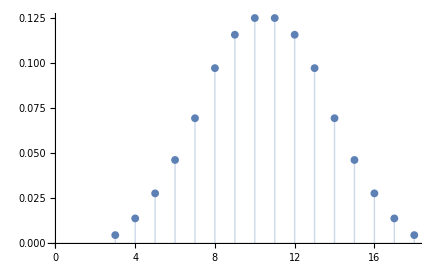

```mathematica
ListPlot[pdf,Filling->Axis]
```

That’s pretty amazing right? We can see that the probability of rolling a sum of 10 or 11 is 25%.

### Summary

This concludes our second lecture on functions. In this lecture, we talked about the Map function and pure functions. This material is used a lot in Mathematica, and in functional programming in general, so it’s important to practice. We’ve provided homework problems to help you get started. We’ll be using these tools a lot when solving problems, so you will probably get a lot of exposure. Over time, this stuff will gel. See you at the next lecture!